## Hamiltonian Construction

### Constructing the TC Hamiltonian

```mathematica
(*Constants*)
bsize=25;ω0=1.0; ωc = 1.0; K = 4;j = 0.07;
(*Identity matrices for TLS and QHO*)
idTSS=SparseArray[IdentityMatrix[2]];
idHO=SparseArray[IdentityMatrix[bsize]];

(*TLS initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{ω0/2,-ω0/2}];
(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*TLS raising and lowering operators*)
σm={{0,0},{1,0}};
σp={{0,1},{0,0}};

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

(*Scaled harmonic oscillator Hamiltonian, using convention with TLS on the left.*)
HTC = KroneckerProduct[IdentityMatrix[2^K], H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Print[Normal[H0TSSi]//MatrixForm];*)
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
HTC+=KroneckerProduct[H0TSSi,idHO];

σpi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σp],Sequence@@rightIds];σmi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σm],Sequence@@rightIds];
HTC+=j*(KroneckerProduct[σpi,a]+KroneckerProduct[σmi,a†]);
,{i,K}];
```

### Constructing the Dicke Hamiltonian

```mathematica
σx = σm + σp;
HD = KroneckerProduct[IdentityMatrix[2^K], H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Print[Normal[H0TSSi]//MatrixForm];*)
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
HD+=KroneckerProduct[H0TSSi,idHO];


σxi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σx],Sequence@@rightIds];
HD+=j*(KroneckerProduct[σxi,a]+KroneckerProduct[σxi,a†]);
,{i,K}];
```

## State, Operator Construction

### Symmetric State Generation

### Initial State

```mathematica
ψ0HO=SparseArray[{1->1.0},bsize];

(*ψ0HO=Table[coeff[n,1,0],{n,0,bsize-1}];*)
(*α=3.5;
ψ0HO=Table[Exp[-Abs[α]^2/2]*(α^n/Sqrt[n!]),{n,0,bsize-1}]; (*in number/fock basis*)
ψ0HO=SparseArray[ψ0HO];*)

(*ψ0Vec = 1/√2 * (KroneckerProduct[{0, 1}, {1, 0},  ψ0HO]
+ KroneckerProduct[{1, 0}, {0, 1},  ψ0HO]) // Flatten
ψ0Vec = KroneckerProduct[{1, 0}, {1, 0}, {1, 0}, {1, 0}, {1, 0}, ψ0HO] // Flatten;*)
(*ψ0Vec = KroneckerProduct[{1, 0}, {1, 0}, ψ0HO] // Flatten;*)
(*ψ0Vec= 1/√6 * ((KroneckerProduct[{1, 0}, {1, 0}, {0, 1}, {0, 1},ψ0HO]) + 
(KroneckerProduct[{1, 0}, {0, 1}, {1, 0}, {0, 1},ψ0HO]) + 
(KroneckerProduct[{1, 0}, {0, 1},  {0, 1},{1, 0},ψ0HO]) + 
(KroneckerProduct[{0, 1}, {1, 0},  {0, 1},{1, 0},ψ0HO])+ 
(KroneckerProduct[{0, 1}, {1, 0},  {1, 0},{0, 1},ψ0HO] )+
(KroneckerProduct[{0, 1}, {0, 1},  {1, 0},{1, 0},ψ0HO])) // Flatten*)
ψ0Vec = 1/2 * (KroneckerProduct[{1, 0}, {0, 1}, {0, 1}, {0, 1},ψ0HO]+ 
KroneckerProduct[{0, 1}, {1, 0}, {0, 1}, {0, 1},ψ0HO]+
KroneckerProduct[{0, 1}, {0, 1}, {1, 0}, {0, 1},ψ0HO]+
KroneckerProduct[{0, 1}, {0, 1}, {0, 1}, {1, 0},ψ0HO]) // Flatten
Print["Norm of initial state: ",Norm[ψ0Vec]];
```

SparseArray[…]

Norm of initial state: 1.

### Operator Construction

```mathematica
(*oscillator position*)
xM=KroneckerProduct[IdentityMatrix[2^K],1/Sqrt[2](a†+a)];
(*number operator and related operators*)
aDaggerA=KroneckerProduct[IdentityMatrix[2^K],a†.a];
aDaggerAsr = aDaggerA.aDaggerA;

(*excited state population*)
excitedStateProjection[i_Integer]:=Module[
{
idTSS=IdentityMatrix[2],
partialExcitedProj={{1,0},{0,0}},
leftIds,rightIds,excitedProj
},
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
excitedProj=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,partialExcitedProj,Sequence@@rightIds], idHO];
excitedProj  (*Return the constructed operator*);
excitedProj]
```

## Propagation

```mathematica
tMax =1000; 
tRange=Range[0,tMax,1];

TCstate[t_] := MatrixExp[-I * HTC * t, ψ0Vec];
ψtc=ParallelTable[TCstate[t],{t,tRange}];

Dstate[t_] := MatrixExp[-I * HD * t, ψ0Vec];
ψd=ParallelTable[Dstate[t],{t,tRange}];
```

## Expected Excited State Populations

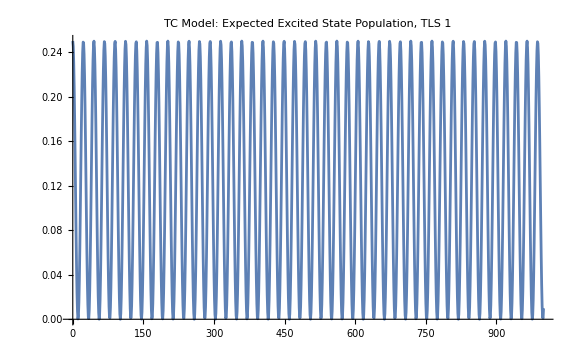

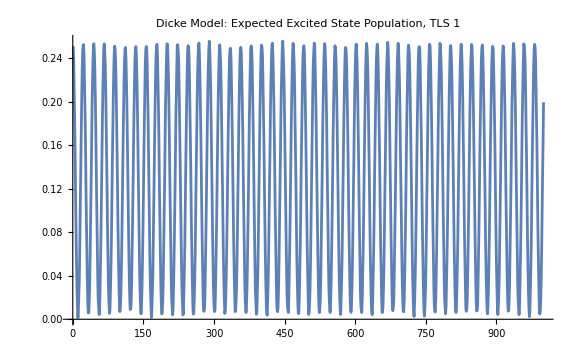

```mathematica
excP1= excitedStateProjection[1];
tcP1=Table[Conjugate[ψtc[[n]]].excP1.ψtc[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,tcP1//Re}//Transpose, ImageSize->Large, 
PlotLabel->"TC Model: Expected Excited State Population, TLS 1"]
dP1=Table[Conjugate[ψd[[n]]].excP1.ψd[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,dP1//Re}//Transpose, ImageSize->Large, 
PlotLabel->"Dicke Model: Expected Excited State Population, TLS 1"]
```

## Photon Statistics

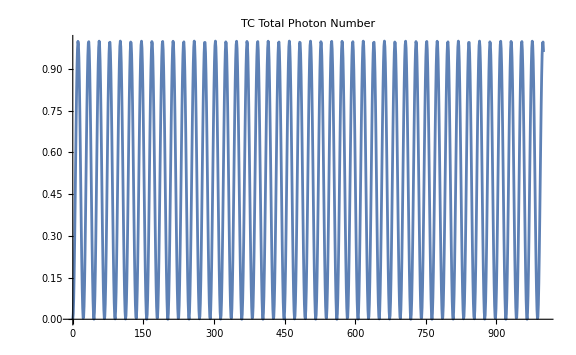

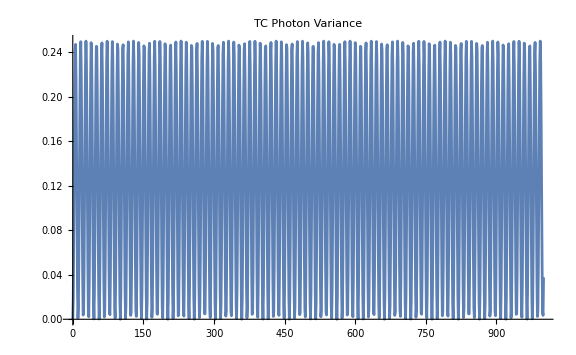

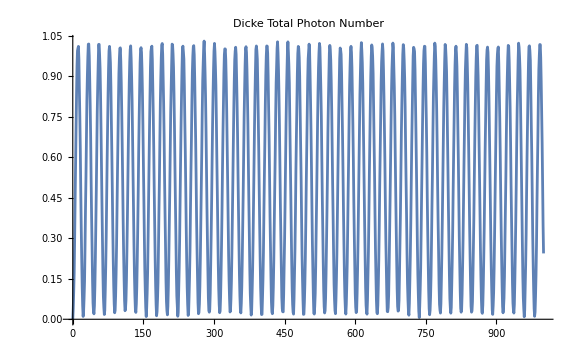

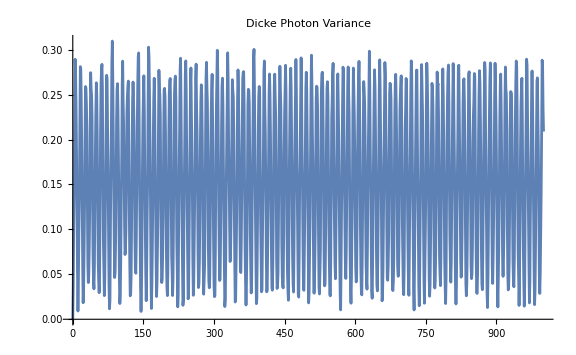

```mathematica
aDaggerA=KroneckerProduct[IdentityMatrix[2^K],a†.a];
aDaggerAsr = aDaggerA.aDaggerA;
photonsTC=Table[Conjugate[ψtc[[n]]].aDaggerA.ψtc[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,photonsTC//Re}//Transpose,PlotRange->All,PlotLabel->"TC Total Photon Number", ImageSize->Large]

newPhotonsTC=Table[Conjugate[ψtc[[n]]].aDaggerAsr.ψtc[[n]],{n,Length@tRange}] - photonsTC^2;
ListLinePlot[{tRange,newPhotonsTC//Re}//Transpose,PlotRange->All,PlotLabel->"TC Photon Variance", ImageSize->Large]

photonsD=Table[Conjugate[ψd[[n]]].aDaggerA.ψd[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,photonsD//Re}//Transpose,PlotRange->All,PlotLabel->"Dicke Total Photon Number", ImageSize->Large]

newPhotonsD=Table[Conjugate[ψd[[n]]].aDaggerAsr.ψd[[n]],{n,Length@tRange}] - photonsD^2;
ListLinePlot[{tRange,newPhotonsD//Re}//Transpose,PlotRange->All,PlotLabel->"Dicke Photon Variance", ImageSize->Large]
```

## Eigenbasis Projection

Eigensystem::arh: Because finding 400 out of the 400 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Min TC: 2.86986×10^-42 Max TC: 0.0567113

Min Dicke: 1.70607×10^-35 Max Dicke: 0.0848863

Mean Squared Error: 0.000124505

Normalized MSE: 1.42795

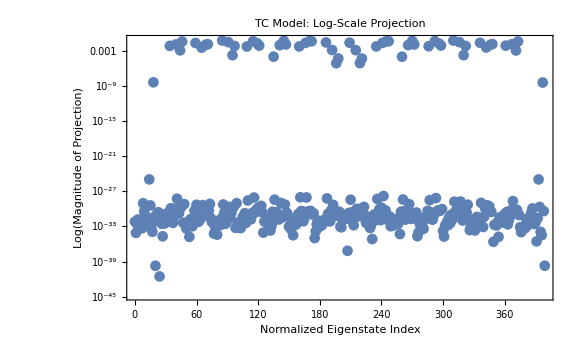

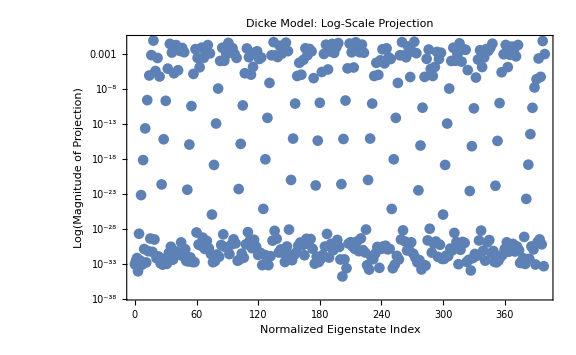

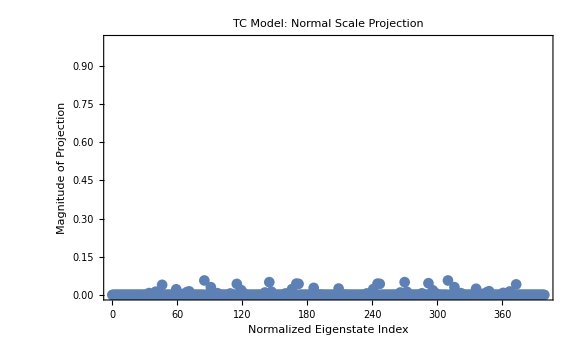

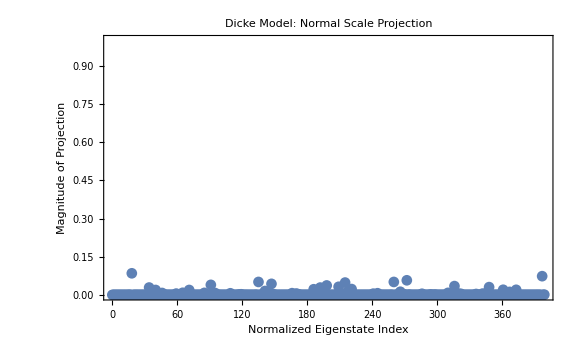

```mathematica
(*Normalize the initial state vector*)
ψ0Vec=Normalize[ψ0Vec];

(*Calculate the eigenvalues and eigenvectors*)
eigensystemTC=Eigensystem[HTC];
eigensystemD=Eigensystem[HD];

(*Sort eigenvalues and eigenvectors in ascending order of eigenvalues*)
sortedEigensystemTC=Transpose[SortBy[Transpose[eigensystemTC],First]];
sortedEigensystemD=Transpose[SortBy[Transpose[eigensystemD],First]];

(*Extract sorted eigenvectors*)
sortedEigenvectorsTC=Normalize/@sortedEigensystemTC[[2]];
sortedEigenvectorsD=Normalize/@sortedEigensystemD[[2]];

(*Project the initial state onto the eigenbasis*)
projectionsTC=Abs[ConjugateTranspose[sortedEigenvectorsTC].ψ0Vec]^2;
projectionsD=Abs[ConjugateTranspose[sortedEigenvectorsD].ψ0Vec]^2;

(*Print diagnostic information*)
Print["Min TC: ",Min[projectionsTC]," Max TC: ",Max[projectionsTC]]
Print["Min Dicke: ",Min[projectionsD]," Max Dicke: ",Max[projectionsD]]

SqDiff=Total[(projectionsTC-projectionsD)^2];
MSE=SqDiff/Length[projectionsD];
VarD=Variance[projectionsD];
NMSE=MSE/VarD;
Print["Mean Squared Error: ", MSE];
Print["Normalized MSE: ", NMSE];

(*Normalize the indices for the horizontal axis*)
nTC=Length[projectionsTC];
nD=Length[projectionsD];
indicesTC=Range[0,nTC-1];
indicesD=Range[0,nD-1];

(*Separate plots for each model with log scale*)
tcLogPlot=ListLogPlot[Transpose[{indicesTC,projectionsTC}],PlotLabel->"TC Model: Log-Scale Projection",AxesLabel->{"Normalized Eigenstate Index","Log(Magnitude of Projection)"},PlotRange->All,Joined->False,PlotMarkers->Automatic,Frame->True,ImageSize->Large]
dickeLogPlot=ListLogPlot[Transpose[{indicesD,projectionsD}],PlotLabel->"Dicke Model: Log-Scale Projection",AxesLabel->{"Normalized Eigenstate Index","Log(Magnitude of Projection)"},PlotRange->All,Joined->False,PlotMarkers->Automatic,Frame->True,ImageSize->Large]

(*Separate plots for each model with normal scale*)
tcPlot=ListPlot[Transpose[{indicesTC,projectionsTC}],PlotLabel->"TC Model: Normal Scale Projection",AxesLabel->{"Normalized Eigenstate Index","Magnitude of Projection"},PlotRange->{0, 1},Joined->False,PlotMarkers->Automatic,Frame->True,ImageSize->Large]
dickePlot=ListPlot[Transpose[{indicesD,projectionsD}],PlotLabel->"Dicke Model: Normal Scale Projection",AxesLabel->{"Normalized Eigenstate Index","Magnitude of Projection"},PlotRange->{0, 1},Joined->False,PlotMarkers->Automatic,Frame->True,ImageSize->Large]
```